# F 5 : Trajectoire et Thermodynamique des acides nucléiques

## 1. Marche aléatoire et Acides nucléiques (SB et DB)

#### A. Construction d’un fragment d’ADN double brin de 10 à 1000 paires de bases.

```mathematica
RandomVariate[NormalDistribution[0,5],{2,2}];
```

```mathematica
Table[RandomVariate[NormalDistribution[0,5],{1}],{x,1,10}]
```

{{3.03077},{-6.85904},{-3.21501},{-6.88511},{-8.05782},{2.94142},{-1.49212},{2.01826},{2.73128},{3.24455}}

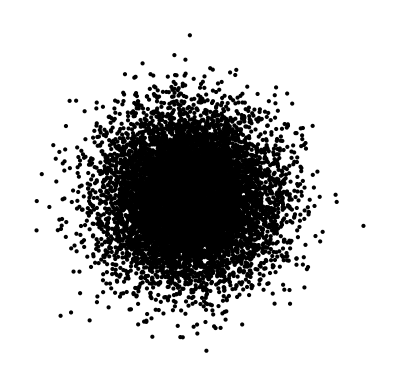

```mathematica
Graphics[{Point[RandomVariate[NormalDistribution[],{10000,2}]]}]
```

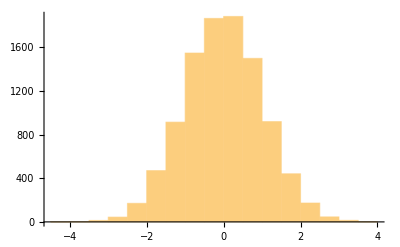

```mathematica
RandomVariate[NormalDistribution[],{10000}]//Histogram
```

```mathematica
npb= 60;
theta[μ_,σ_,length_]:=RandomVariate[NormalDistribution[μ,σ],{length+1}];
theta[0Degree,5Degree,npb]
```

{-0.136806,-0.18195,-0.0675804,-0.0229741,-0.127719,-0.0606493,-0.0294339,-0.0187551,-0.0100707,0.0978446,0.0300096,0.166171,-0.135152,-0.0783143,0.0399927,0.133781,-0.15264,0.0432409,0.0798767,-0.0041397,0.194795,0.109385,-0.111973,0.129851,0.0530644,0.150053,0.0574686,-0.0142627,0.0237229,0.0417067,-0.0534456,-0.113677,0.0304763,0.0954483,-0.069869,-0.0680014,0.0785079,-0.0244402,0.0388457,-0.0607768,0.0407874,0.0289465,-0.0465466,0.048232,0.0708854,0.0370181,-0.0201109,-0.334037,0.0678103,-0.00801849,-0.036129,0.15794,-0.0827573,-0.0565854,-0.0126057,0.0196153,-0.0186553,-0.0348566,-0.110873,-0.0531252,0.0500746}

```mathematica
thetas[μ_,σ_,length_]:=(FoldList[Plus,0,theta[μ,σ,length]]);
```

```mathematica
tiadn[μ_,σ_,length_]:=(Table[{Sin[θ],Cos[θ]},{θ,thetas[μ,σ,length]}]);
```

```mathematica
tjadn[μ_,σ_,length_]:=FoldList[Plus,{0,0},tiadn[μ,σ,length]];
```

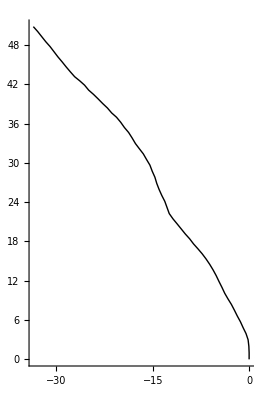

```mathematica
Show[Graphics[Line[tjadn[0Degree,5Degree,npb]]],Axes->True]
```

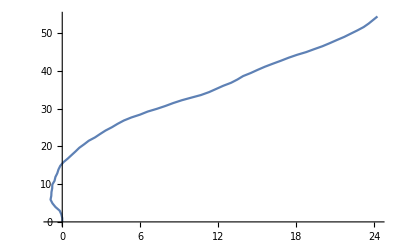

```mathematica
ListPlot[tjadn[0Degree,5Degree,npb],Joined->True]
```

#### B. Application : Visualisation d’un petit oligonucléotide “quasiment droit”, et “courbes”

```mathematica
tjadnList[μ_,σ_,length_,imax_]:=Table[tjadn[μ,σ,length],{i,imax}];
```

{{{0,0},{0,1},{-0.0939932,1.99557},{-0.374168,2.95552},{-0.584879,3.93307},{-0.754312,4.91861},{-0.894455,5.90874},{-1.00164,6.90298},{-1.15027,7.89188},{-1.19492,8.89088},{-1.34349,9.87978},{-1.59731,10.847},{-1.81636,11.8227}},{{0,0},{0,1},{-0.113988,1.99348},{-0.20408,2.98942},{-0.276799,3.98677},{-0.521295,4.95642},{-0.633885,5.95006},{-0.653889,6.94986},{-0.558519,7.9453},{-0.287395,8.90785},{0.0360749,9.85408},{0.325423,10.8113},{0.71233,11.7334}}}

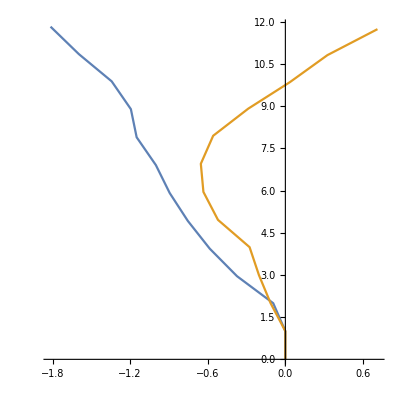

```mathematica
tjs=Table[tjadn[0Degree,5Degree,10],{i,2}]
ListPlot[tjs,AspectRatio->1.,Axes->Automatic,Joined->True]
```

```mathematica
Manipulate[ListPlot[Table[tjadn[0,σ,length],{x}],Joined->True,AspectRatio->1.,Axes->Automatic],{σ,2Degree,10Degree},{length,2,150,1},{x,1,100,1}]
```

Discusion de voir un cicle à partir de quelle taille ? 
On peut voir le tourne d’un brin comme une marche random suivant la loi normal, voir le lengeur comme le pas ou le temps de la marche random. 
La distance est 2π, Esperance est 0, le lengeur de chaque pas est la valeur de σ dans le graphe de manipulate
Donc 1/(√(2π)σ)e^(-1/2((x-μ)/σ)^2)

#### C. Construction de grands ADN